```mathematica
Quit[]
```

```mathematica
(*Asyntotic analysis*)
```

```mathematica
Systema={1/(r^2 g[r]^5)N[r]^2 (Subscript[α, GR] g[r]^2 (-g[r]+g[r]^3+2 r g'[r])+1/Mp^2 8 Subscript[α, GB] (-g[r] (-1+g[r]^2) ϕ'[r]^2 f''[ϕ[r]]+f'[ϕ[r]] ((-3+g[r]^2) g'[r] ϕ'[r]-g[r] (-1+g[r]^2) ϕ''[r])))-(N[r]^2 (2 (1+ϵ) ρ[r]+2 Subscript[α, ϕ] m^2 ϕ[r]^2+(Subscript[α, ϕ] ϕ'[r]^2)/g[r]^2))/(2 Mp^2),(Subscript[α, GR] (N[r]-g[r]^2 N[r]+2 r N'[r])+(8 Subscript[α, GB] (-3+g[r]^2) f'[ϕ[r]] N'[r] ϕ'[r])/(Mp^2 g[r]^2))/(r^2 N[r])-(2 g[r]^2 (P[r]-Subscript[α, ϕ] m^2 ϕ[r]^2)+Subscript[α, ϕ] ϕ'[r]^2)/(2 Mp^2),1/(2 Mp^2)r (r (-2 P[r]+2 Subscript[α, ϕ] m^2 ϕ[r]^2+(Subscript[α, ϕ] ϕ'[r]^2)/g[r]^2)+1/(g[r]^5 N[r])2 (-Subscript[α, GR] Mp^2 g[r]^2 g'[r] (N[r]+r N'[r])+24 Subscript[α, GB] f'[ϕ[r]] g'[r] N'[r] ϕ'[r]+Subscript[α, GR] Mp^2 g[r]^3 (N'[r]+r N''[r])-8 Subscript[α, GB] g[r] (f'[ϕ[r]] ϕ'[r] N''[r]+N'[r] (ϕ'[r]^2 f''[ϕ[r]]+f'[ϕ[r]] ϕ''[r])))),(8 Subscript[α, GB] f'[ϕ[r]] ((-3+g[r]^2) g'[r] N'[r]-g[r] (-1+g[r]^2) N''[r]))/(r^2 g[r]^5 N[r])+Subscript[α, ϕ] (-2 m^2 ϕ[r]+(-g'[r] ϕ'[r]+g[r] ((2/r+N'[r]/N[r]) ϕ'[r]+ϕ''[r]))/g[r]^3)}/.fuc->f/.mS->0/.ka->Mp^2;
```

```mathematica
AnsF=f->Function[x, β x^2/2];
```

```mathematica
(*Field Equations, at the infinite p,ρ  are zero*)
eq1=Systema[[1]]/.{den[r]->0, pres[r]->0,AnsF}//ExpandAll//Simplify;
eq2=Systema[[2]]/.{den[r]->0, pres[r]->0,AnsF}//ExpandAll//Simplify;
eq3=Systema[[3]]/.{den[r]->0, pres[r]->0,AnsF}//ExpandAll//Simplify;
eq4=Systema[[4]]/.{den[r]->0, pres[r]->0,AnsF}//ExpandAll//Simplify;
```

```mathematica
(*Anzats*)
PhiAnsatz=ϕ->Function[x,∑_(i=0)^7 Subscript[a, i]/x^i]; 
NAnsatz=NN->Function[x,√(1+∑_(i=1)^7 Subscript[n, i]/x^i)]; 
gAnsatz=gg->Function[x,√(1/(1+∑_(i=1)^7 Subscript[g, i]/x^i))];
```

```mathematica
(*Serie*)
ESeq00=Series[eq1/.PhiAnsatz/.NAnsatz/.gAnsatz,{r,Infinity,8}];
ESeq11=Series[eq2/.PhiAnsatz/.NAnsatz/.gAnsatz,{r,Infinity,8}];
ESeq22=Series[eq3/.PhiAnsatz/.NAnsatz/.gAnsatz,{r,Infinity,8}];
ESeq33=Series[eq4/.PhiAnsatz/.NAnsatz/.gAnsatz,{r,Infinity,8}];
```

```mathematica
(*Ord*)
Om4Seq00=Coefficient[ESeq00,r,-4]//Simplify;
Om5Seq00=Coefficient[ESeq00,r,-5]//Simplify;
Om6Seq00=Coefficient[ESeq00,r,-6]//Simplify;
Om7Seq00=Coefficient[ESeq00,r,-7]//Simplify;
Om8Seq00=Coefficient[ESeq00,r,-8]//Simplify;
```

```mathematica
Om3Seq11=Coefficient[ESeq11,r,-3]//Simplify;
Om4Seq11=Coefficient[ESeq11,r,-4]//Simplify;
Om5Seq11=Coefficient[ESeq11,r,-5]//Simplify;
Om6Seq11=Coefficient[ESeq11,r,-6]//Simplify;
Om7Seq11=Coefficient[ESeq11,r,-7]//Simplify;
```

```mathematica
Om1Seq22=Coefficient[ESeq22,r,-1]//Simplify;
Om2Seq22=Coefficient[ESeq22,r,-2]//Simplify;
Om3Seq22=Coefficient[ESeq22,r,-3]//Simplify;
Om4Seq22=Coefficient[ESeq22,r,-4]//Simplify;
Om5Seq22=Coefficient[ESeq22,r,-5]//Simplify;
```

```mathematica
Om4Seq33=Coefficient[ESeq33,r,-4]//Simplify;
Om5Seq33=Coefficient[ESeq33,r,-5]//Simplify;
Om6Seq33=Coefficient[ESeq33,r,-6]//Simplify;
Om7Seq33=Coefficient[ESeq33,r,-7]//Simplify;
Om8Seq33=Coefficient[ESeq33,r,-8]//Simplify;
```

```mathematica
(*Resolviendo*)
sol0=Last@Solve[{Om3Seq11==0,Om4Seq33==0,Om4Seq00==0},{Subscript[n, 1],Subscript[a, 2],Subscript[g, 2]}]//Simplify
sol1=Last@Solve[{Om4Seq11==0,Om5Seq33==0,Om5Seq00==0}/.sol0,{Subscript[n, 2],Subscript[a, 3],Subscript[g, 3]}]//Simplify
sol2=Last@Solve[{Om5Seq11==0,Om6Seq33==0,Om6Seq00==0}/.sol0/.sol1,{Subscript[n, 3],Subscript[a, 4],Subscript[g, 4]}]//Simplify
sol3=Last@Solve[{Om6Seq11==0,Om7Seq33==0,Om7Seq00==0}/.sol0/.sol1/.sol2,{Subscript[n, 4],Subscript[a, 5],Subscript[g, 5]}]//Simplify
sol4=Last@Solve[{Om7Seq11==0,Om8Seq33==0,Om8Seq00==0}/.sol0/.sol1/.sol2/.sol3,{Subscript[n, 5],Subscript[a, 6],Subscript[g, 6]}]//Simplify
```

{n_1→g_1,a_2→-1/2 a_1 g_1,g_2→(aPhi a_1^2)/(2 aRG Mp^2)}

{n_2→0,a_3→-(aPhi a_1^3)/(12 aRG Mp^2)+1/3 a_1 g_1^2,g_3→-(aPhi a_1^2 g_1)/(4 aRG Mp^2)}

{n_3→-(aPhi a_1^2 g_1)/(12 aRG Mp^2),a_4→(aPhi a_1^3 g_1)/(6 aRG Mp^2)-(aGB β a_0 g_1^2)/aPhi-1/4 a_1 g_1^3,g_4→(a_1 g_1 (-48 aGB β a_0+aPhi a_1 g_1))/(6 aRG Mp^2)}

{n_4→(a_1 g_1 (-48 aGB β a_0+aPhi a_1 g_1))/(12 aRG Mp^2),a_5→1/480 ((9 aPhi^2 a_1^5)/(aRG^2 Mp^4)+(384 aGB β a_0 a_1^2 g_1)/(aRG Mp^2)-(116 aPhi a_1^3 g_1^2)/(aRG Mp^2)+(384 aGB β a_0 g_1^3)/aPhi+96 a_1 g_1^2 (-(3 aGB β)/aPhi+g_1^2)),g_5→(a_1^2 (-384 aGB aPhi β a_0 a_1+g_1 (aPhi^2 a_1^2-12 aRG Mp^2 (64 aGB β+aPhi g_1^2))))/(96 aRG^2 Mp^4)}

{n_5→(a_1 (-128 aGB β a_0 (aPhi a_1^2-aRG Mp^2 g_1^2)+a_1 g_1 (3 aPhi^2 a_1^2-4 aRG Mp^2 (128 aGB β+3 aPhi g_1^2))))/(160 aRG^2 Mp^4),a_6→(8 aGB β a_0 (6 aPhi^2 a_1^4-21 aPhi aRG Mp^2 a_1^2 g_1^2-10 aRG^2 Mp^4 g_1^4)+a_1 g_1 (-8 aPhi^3 a_1^4+4 aRG^2 Mp^4 g_1^2 (21 aGB β-5 aPhi g_1^2)+aPhi aRG Mp^2 a_1^2 (80 aGB β+37 aPhi g_1^2)))/(120 aPhi aRG^2 Mp^4),g_6→(a_1^2 (48 aGB aPhi β a_0 a_1 g_1+4 aRG Mp^2 g_1^2 (42 aGB β+aPhi g_1^2)-aPhi a_1^2 (160 aGB β+aPhi g_1^2)))/(40 aRG^2 Mp^4)}

```mathematica
Collect[(ϕ[r]/.PhiAnsatz)/.sol0/.sol1/.sol2/.sol3/.sol4/.Subscript[a, 7]->0,{r, Subscript[a, 0],Subscript[a, 1],Subscript[g, 1]},FullSimplify]
Collect[(NN[r]/.NAnsatz)/.sol0/.sol1/.sol2/.sol3/.sol4/.Subscript[a, 7]->0,{r, Subscript[a, 0],Subscript[a, 1],Subscript[g, 1]},FullSimplify]
Collect[(gg[r]/.gAnsatz)/.sol0/.sol1/.sol2/.sol3/.sol4/.Subscript[a, 7]->0,{r, Subscript[a, 0],Subscript[a, 1],Subscript[g, 1]},FullSimplify]
```

a_0+a_1/r-(a_1 g_1)/(2 r^2)+(-(aPhi a_1^3)/(12 aRG Mp^2)+1/3 a_1 g_1^2)/r^3+((aPhi a_1^3 g_1)/(6 aRG Mp^2)-(aGB β a_0 g_1^2)/aPhi-1/4 a_1 g_1^3)/r^4+((3 aPhi^2 a_1^5)/(160 aRG^2 Mp^4)-(29 aPhi a_1^3 g_1^2)/(120 aRG Mp^2)+a_0 ((4 aGB β a_1^2 g_1)/(5 aRG Mp^2)+(4 aGB β g_1^3)/(5 aPhi))+a_1 (-(3 aGB β g_1^2)/(5 aPhi)+g_1^4/5))/r^5+(-(aPhi^2 a_1^5 g_1)/(15 aRG^2 Mp^4)+a_1^3 ((2 aGB β g_1)/(3 aRG Mp^2)+(37 aPhi g_1^3)/(120 aRG Mp^2))+a_0 ((2 aGB aPhi β a_1^4)/(5 aRG^2 Mp^4)-(7 aGB β a_1^2 g_1^2)/(5 aRG Mp^2)-(2 aGB β g_1^4)/(3 aPhi))+a_1 ((7 aGB β g_1^3)/(10 aPhi)-g_1^5/6))/r^6

(√((480 r^6 (r+g_1)+(r^2 a_1 (-384 aGB β a_0 (aPhi a_1^2+aRG Mp^2 (5 r-g_1) g_1)+a_1 g_1 (9 aPhi^2 a_1^2-4 aRG Mp^2 (10 aPhi r^2+384 aGB β+aPhi g_1 (-10 r+9 g_1)))))/(aRG^2 Mp^4)+480 r n_6+480 n_7)/r^7))/(4 √30)

4 √30 √((aRG^2 Mp^4 r^7)/(-3840 aGB aRG Mp^2 r^3 β a_0 a_1 g_1+192 aGB aPhi r β a_0 a_1^3 (-10 r+3 g_1)+aPhi r a_1^4 (-1920 aGB β+aPhi (5 r-12 g_1) g_1)+4 aRG Mp^2 r a_1^2 (60 aPhi r^4+g_1 (-30 (aPhi r^3+32 aGB r β)+g_1 (20 aPhi r^2+504 aGB β+3 aPhi g_1 (-5 r+4 g_1))))+480 aRG^2 Mp^4 (r^6 (r+g_1)+g_7)))

```mathematica
(*soluciones en rMax*)
```

```mathematica
ϕRmax=Subscript[a, 1]^5 ((3 aPhi^2)/(160 aRG^2 Mp^4 r^5)-(aPhi^2 Subscript[g, 1])/(15 aRG^2 Mp^4 r^6))+Subscript[a, 1]^3 (-aPhi/(12 aRG Mp^2 r^3)+((aPhi r^2+4 aGB β) Subscript[g, 1])/(6 aRG Mp^2 r^6)-(29 aPhi Subscript[g, 1]^2)/(120 aRG Mp^2 r^5)+(37 aPhi Subscript[g, 1]^3)/(120 aRG Mp^2 r^6))+Subscript[a, 1] (1/r-Subscript[g, 1]/(2 r^2)+(1/(3 r^3)-(3 aGB β)/(5 aPhi r^5)) Subscript[g, 1]^2+(-1/(4 r^4)+(7 aGB β)/(10 aPhi r^6)) Subscript[g, 1]^3+Subscript[g, 1]^4/(5 r^5)-Subscript[g, 1]^5/(6 r^6))+Subscript[a, 0] (1+(2 aGB aPhi β Subscript[a, 1]^4)/(5 aRG^2 Mp^4 r^6)-(aGB β Subscript[g, 1]^2)/(aPhi r^4)+(4 aGB β Subscript[g, 1]^3)/(5 aPhi r^5)-(2 aGB β Subscript[g, 1]^4)/(3 aPhi r^6)+Subscript[a, 1]^2 ((4 aGB β Subscript[g, 1])/(5 aRG Mp^2 r^5)-(7 aGB β Subscript[g, 1]^2)/(5 aRG Mp^2 r^6)))/.{aRG->1,aPhi->1,aGB->1};
dϕRmax=D[ϕRmax,r]//FullSimplify;
gRmax=4 √30 √((aRG^2 Mp^4 r^6)/(-192 aGB aPhi β Subscript[a, 0] Subscript[a, 1]^3 (10 r-3 Subscript[g, 1])-3840 aGB aRG Mp^2 r^2 β Subscript[a, 0] Subscript[a, 1] Subscript[g, 1]+480 aRG^2 Mp^4 r^5 (r+Subscript[g, 1])+aPhi Subscript[a, 1]^4 (-1920 aGB β+5 aPhi r Subscript[g, 1]-12 aPhi Subscript[g, 1]^2)+4 aRG Mp^2 Subscript[a, 1]^2 (60 aPhi r^4-30 (aPhi r^3+32 aGB r β) Subscript[g, 1]+4 (5 aPhi r^2+126 aGB β) Subscript[g, 1]^2-15 aPhi r Subscript[g, 1]^3+12 aPhi Subscript[g, 1]^4)))/.{aRG->1,aPhi->1,aGB->1};
nRmax=(√((480 aRG^2 Mp^4 r^5+(480 aRG^2 Mp^4 r^4-8 aRG Mp^2 (5 aPhi r^2+192 aGB β) Subscript[a, 1]^2+9 aPhi^2 Subscript[a, 1]^4) Subscript[g, 1]+40 aPhi aRG Mp^2 r Subscript[a, 1]^2 Subscript[g, 1]^2-36 aPhi aRG Mp^2 Subscript[a, 1]^2 Subscript[g, 1]^3-384 aGB β Subscript[a, 0] Subscript[a, 1] (aPhi Subscript[a, 1]^2+aRG Mp^2 (5 r-Subscript[g, 1]) Subscript[g, 1]))/(aRG^2 Mp^4 r^5)))/(4 √30)/.{aRG->1,aPhi->1,aGB->1};
dnRmax=D[nRmax,r]//Simplify;
```

```mathematica
(*Chek Escalamiento*)
```

```mathematica
rules={ϕ[r]-> λ ϕ[x],β ->β/λ^2,gg[r]->gg[x],NN[r]->NN[x]};
ruleD=Derivative[n_][variab_][r]:>If[variab===φ,λ^(n+1)Derivative[n][variab][x],λ^n Derivative[n][variab][x]];
ruleG[exp_]:=(exp/.rules/.ruleD/.r->x/λ)/.x->r;
ruleSerie={Subscript[a, 0]->λ Subscript[a, 0],Subscript[a, 1] ->λ Subscript[a, 1]/λ,Subscript[g, 1]->Subscript[g, 1]/λ};
```

```mathematica
((ϕRmax//ruleG)/λ/.ruleSerie/.λ->c1 Mp )//Expand
```

a_0+a_1/r-(c1^2 a_1^3)/(12 r^3)+(2 c1^4 β a_0 a_1^4)/(5 r^6)+(3 c1^4 a_1^5)/(160 r^5)-(a_1 g_1)/(2 r^2)+(4 c1^2 β a_0 a_1^2 g_1)/(5 r^5)+(c1^2 a_1^3 g_1)/(6 r^4)+(2 c1^2 β a_1^3 g_1)/(3 r^6)-(c1^4 a_1^5 g_1)/(15 r^6)-(β a_0 g_1^2)/r^4+(a_1 g_1^2)/(3 r^3)-(3 β a_1 g_1^2)/(5 r^5)-(7 c1^2 β a_0 a_1^2 g_1^2)/(5 r^6)-(29 c1^2 a_1^3 g_1^2)/(120 r^5)+(4 β a_0 g_1^3)/(5 r^5)-(a_1 g_1^3)/(4 r^4)+(7 β a_1 g_1^3)/(10 r^6)+(37 c1^2 a_1^3 g_1^3)/(120 r^6)-(2 β a_0 g_1^4)/(3 r^6)+(a_1 g_1^4)/(5 r^5)-(a_1 g_1^5)/(6 r^6)

```mathematica
ϕRmax/.Mp->1/c1//Expand
```

a_0+a_1/r-(c1^2 a_1^3)/(12 r^3)+(2 c1^4 β a_0 a_1^4)/(5 r^6)+(3 c1^4 a_1^5)/(160 r^5)-(a_1 g_1)/(2 r^2)+(4 c1^2 β a_0 a_1^2 g_1)/(5 r^5)+(c1^2 a_1^3 g_1)/(6 r^4)+(2 c1^2 β a_1^3 g_1)/(3 r^6)-(c1^4 a_1^5 g_1)/(15 r^6)-(β a_0 g_1^2)/r^4+(a_1 g_1^2)/(3 r^3)-(3 β a_1 g_1^2)/(5 r^5)-(7 c1^2 β a_0 a_1^2 g_1^2)/(5 r^6)-(29 c1^2 a_1^3 g_1^2)/(120 r^5)+(4 β a_0 g_1^3)/(5 r^5)-(a_1 g_1^3)/(4 r^4)+(7 β a_1 g_1^3)/(10 r^6)+(37 c1^2 a_1^3 g_1^3)/(120 r^6)-(2 β a_0 g_1^4)/(3 r^6)+(a_1 g_1^4)/(5 r^5)-(a_1 g_1^5)/(6 r^6)

```mathematica
%-%%//Simplify
```

0

```mathematica
(*numerical solution para vacio*)
```

```mathematica
ClearAll[rMax, βet,β ,ϕrMax,g1, a1,c1]
EqsList={};
BCList={};
CoefFunctionsList={};
```

```mathematica
AppendTo[CoefFunctionsList,{NN,gg,φ,φ'}];
AppendTo[EqsList,{Systema[[1]]==0,Systema[[3]]==0,Systema[[4]]==0}/.{den[r]->0, pres[r]->0,AnsF}/.{aRG->1,aPhi->1,aGB->1,Mp->1/c1}];
AppendTo[BCList,{NN[rMax]==nRmax,NN'[rMax]==dnRmax, gg[rMax] ==gRmax, φ[rMax]==ϕRmax,φ'[rMax]==dϕRmax }/.{Subscript[g, 1]->g1,Subscript[a, 0]->ϕrMax,Subscript[a, 1] ->a1,r->rMax,Mp->1/c1}];
```

```mathematica
(*Ejemplo*)
ClearAll[rMin,rMax,βet, β ,ϕrMax,g1, c1]

rMin=10^-2;(*10^-2*)
rMax=20;
βet =1.;
ϕrMax=0.01;
a1=1;
g1=-1.6;
dr=10;
c1=1(*1*);

s=NDSolve[{EqsList[[1]],BCList[[1]]}/.β->βet,CoefFunctionsList[[1]],{r,rMin,rMax+dr},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All]
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…],φ'→InterpolatingFunction[…]}}

```mathematica
c2=Sqrt[0.5];
βet2=βet*c2^2
rMin2=rMin*c2
rMax2 =rMax*c2
ϕrMax2=ϕrMax/c2
g12=g1*c2
a12=a1
```

0.5

0.00707107

14.1421

0.0141421

-1.13137

1

```mathematica
ClearAll[rMax, βet,β ,ϕrMax,g1, a1,c1]
EqsList={};
BCList={};
CoefFunctionsList={};
```

```mathematica
AppendTo[CoefFunctionsList,{NN,gg,φ,φ'}];
AppendTo[EqsList,{Systema[[1]]==0,Systema[[3]]==0,Systema[[4]]==0}/.{den[r]->0, pres[r]->0,AnsF}/.{aRG->1,aPhi->1,aGB->1,Mp->1/c2}];
AppendTo[BCList,{NN[rMax2]==nRmax,NN'[rMax2]==dnRmax, gg[rMax2] ==gRmax, φ[rMax2]==ϕRmax,φ'[rMax2]==dϕRmax }/.{Subscript[g, 1]->g12,Subscript[a, 0]->ϕrMax2,Subscript[a, 1] ->a12,r->rMax2,Mp->1/c2}];
```

```mathematica
dr=10;

s2=NDSolve[{EqsList[[1]],BCList[[1]]}/.β->βet2,CoefFunctionsList[[1]],{r,rMin2,rMax2+dr},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All]
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…],φ'→InterpolatingFunction[…]}}

```mathematica
(*Libertad de escalamiento*)
```

```mathematica
{NN[r]/.s,NN[r*c2]/.s2}/.{r->15}
{NN'[r]/.s,c2 NN'[r*c2]/.s2}/.{r->15}
{gg[r]/.s,gg[r*c2]/.s2}/.{r->15}
{φ[r]/.s,c2 φ[r*(c2)]/.s2}/.{r->15}
{φ''[r]/.s,c2^3 φ''[r*(c2)]/.s2}/.{r->15}
{φ'[r]/.s,c2^2 φ'[r*(c2)]/.s2}/.{r->15}
```

{{0.945191},{0.945191}}

{{0.00375546},{0.00375545}}

{{1.05662},{1.05662}}

{{0.0804636},{0.0804634}}

{{0.000700646},{0.000700641}}

{{-0.00496753},{-0.00496749}}

```mathematica
(*Masa*)
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

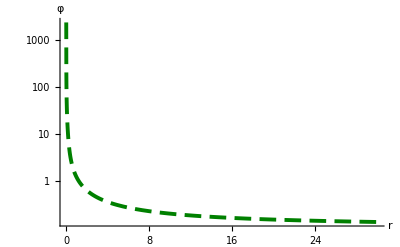
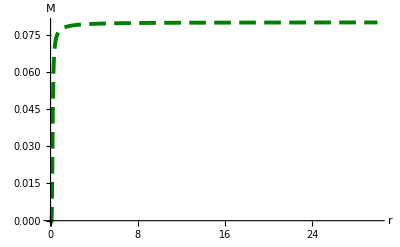
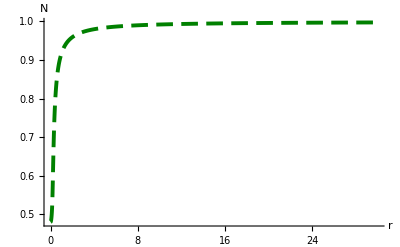
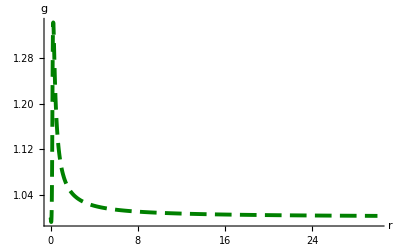

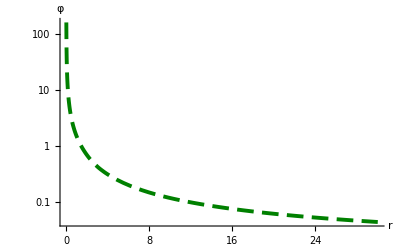
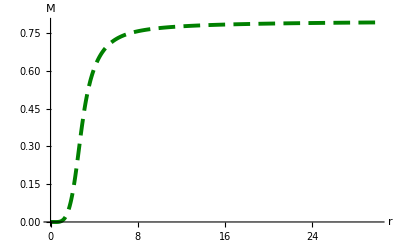
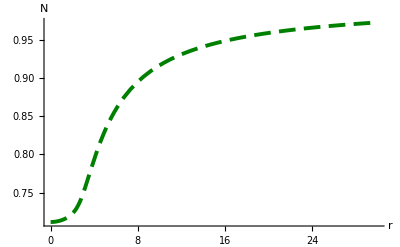
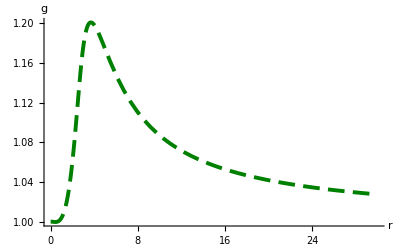

```mathematica
ele={φ[r], M[r],NN[r],gg[r]};
eleLab={"φ", "M", "N", "g"};
Table[If[i==1,LogPlot[{Abs@Evaluate[ele[[i]]/.s]},{r,rMin,rMax+dr},Background->White,PlotRange->{ {0,rMax+dr},All},
AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150}],Plot[{Evaluate[ele[[i]]/.s]},{r,rMin,rMax+dr},Background->White,PlotRange->{ {0,rMax+dr},All},
AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150},AxesOrigin->{0,0}]],{i,4}]
```

```mathematica
(*Ricci*)
RicciScalarEq=Collect[(2 (g[r]^3 N[r]+r g'[r] (2 N[r]+r N'[r])-g[r] (N[r]+r (2 N'[r]+r N''[r]))))/(g[r]^3 N[r] r^2)/.r[]->r,gg[r],Expand];
```

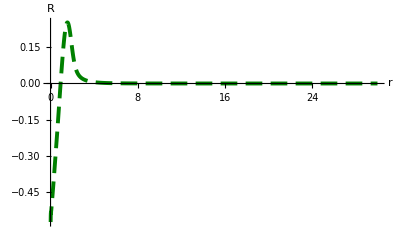

```mathematica
R1=Plot[{Evaluate[RicciScalarEq/.s]},{r,rMin,rMax+dr},Background->White,PlotRange->{ {0,rMax+dr},All},
AxesLabel->{"r","R"},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150}]
```

```mathematica
(*valor teorico*)
-9./(16β)/.β->βet
```

-0.5625

```mathematica
(*densidad de energía effectiva*)
ddphiddN=Solve[{Systema[[3]]==0,Systema[[4]]==0}/.{den[r]->0, pres[r]->0,AnsF}/.{ aRG->1,aPhi->1,Mp->1,aGB->1}, {φ''[r], NN''[r]}]//ExpandAll//Simplify;
ρEff=(NN[r]^2 (-gg[r] (-16 aGB β+(aPhi r^2+16 aGB β) gg[r]^2) φ'[r]^2+16 aGB β φ[r] ((-3+gg[r]^2) gg'[r] φ'[r]-gg[r] (-1+gg[r]^2) φ''[r])))/(2 Mp^2 r^2 gg[r]^5)/.{aRG->1,aPhi->1,Mp->1,aGB->1}//FullSimplify
ρEff2=ρEff/.ddphiddN//FullSimplify//Expand;
```

(NN[r]^2 (-gg[r] (-16 β+(r^2+16 β) gg[r]^2) φ'[r]^2+16 β φ[r] ((-3+gg[r]^2) gg'[r] φ'[r]-gg[r] (-1+gg[r]^2) φ''[r])))/(2 r^2 gg[r]^5)

```mathematica
(3 NN[rMin]^2)/(16 β)/.β->βet/.s
```

{0.0189742}

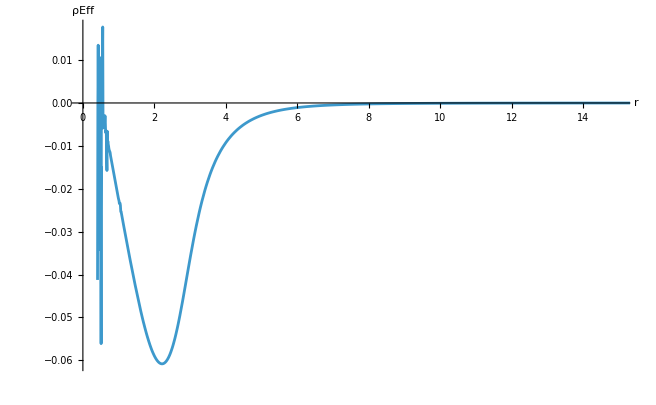

```mathematica
R2=Plot[{Evaluate[ρEff2/.β->βet/.s]},{r,rMin+0.4,rMax+dr},Background->White,PlotRange->{ {0,15},All},
AxesLabel->{"r","ρEff"},ImageSize->{Automatic,150}]
```

```mathematica
(*Series origen*)
sN[r_]:=NN[rMin]+(aPhi r^2 NN[rMin])/(64 aGB β)-(aPhi r^3 NN[rMin] Subscript[a, 0])/(96 aGB β Subscript[a, -1])+(aPhi r^4 NN[rMin] (-aPhi Subscript[a, -1]^2+8 aGB β Subscript[a, 0]^2))/(1024 aGB^2 β^2 Subscript[a, -1]^2)+(aPhi r^5 NN[rMin] Subscript[a, 0] (231 aPhi^2 Subscript[a, -1]^4+6784 aGB aPhi β Subscript[a, -1]^2 Subscript[a, 0]^2-49152 aGB^2 β^2 Subscript[a, 0]^4))/(122880 aGB^2 β^2 Subscript[a, -1]^3 (-3 aPhi Subscript[a, -1]^2+64 aGB β Subscript[a, 0]^2))-(aPhi r^6 NN[rMin] (249 aPhi^3 Subscript[a, -1]^6-393216 aGB^3 β^3 Subscript[a, 0]^6+128 aGB aPhi β Subscript[a, -1]^4 (-36 aRG Mp^2+5 aPhi Subscript[a, 0]^2)+1024 aGB^2 β^2 Subscript[a, -1]^2 Subscript[a, 0]^2 (96 aRG Mp^2+41 aPhi Subscript[a, 0]^2)))/(1179648 aGB^3 β^3 Subscript[a, -1]^4 (-3 aPhi Subscript[a, -1]^2+64 aGB β Subscript[a, 0]^2))/.aPhi->1/.Mp->1/.aRG->1/.aGB->1;
sG[r_]:=1-(aPhi r^2)/(32 aGB β)-(aPhi r^5 Subscript[a, 0] (-5 aPhi Subscript[a, -1]^2+32 aGB β Subscript[a, 0]^2) (-27 aPhi Subscript[a, -1]^2+128 aGB β Subscript[a, 0]^2))/(4096 aGB^2 β^2 Subscript[a, -1]^3 (-3 aPhi Subscript[a, -1]^2+64 aGB β Subscript[a, 0]^2))-(r^3 (81 aPhi^2 Subscript[a, -1]^2 Subscript[a, 0]-384 aGB aPhi β Subscript[a, 0]^3))/(6 (192 aGB aPhi β Subscript[a, -1]^3-4096 aGB^2 β^2 Subscript[a, -1] Subscript[a, 0]^2))+(aPhi r^4 (-3 aPhi^2 Subscript[a, -1]^4-44 aGB aPhi β Subscript[a, -1]^2 Subscript[a, 0]^2+512 aGB^2 β^2 Subscript[a, 0]^4))/(512 aGB^2 β^2 Subscript[a, -1]^2 (-3 aPhi Subscript[a, -1]^2+64 aGB β Subscript[a, 0]^2))+(aPhi r^6 (-621 aPhi^4 Subscript[a, -1]^8+25165824 aGB^4 β^4 Subscript[a, 0]^8+65536 aGB^3 β^3 Subscript[a, -1]^2 Subscript[a, 0]^4 (96 aRG Mp^2-157 aPhi Subscript[a, 0]^2)+3072 aGB^2 aPhi β^2 Subscript[a, -1]^4 Subscript[a, 0]^2 (-192 aRG Mp^2+259 aPhi Subscript[a, 0]^2)+72 aGB aPhi^2 β Subscript[a, -1]^6 (192 aRG Mp^2+287 aPhi Subscript[a, 0]^2)))/(393216 aGB^3 β^3 Subscript[a, -1]^4 (3 aPhi Subscript[a, -1]^2-64 aGB β Subscript[a, 0]^2)^2)/.aPhi->1/.Mp->1/.aRG->1/.aGB->1;

sϕ[r_]:=Subscript[a, -1]/r+(3 aPhi r Subscript[a, -1])/(128 aGB β)+Subscript[a, 0]+(aPhi^2 r^3 Subscript[a, -1] (69 aPhi Subscript[a, -1]^2-128 aGB β Subscript[a, 0]^2))/(98304 aGB^2 β^2 (-3 aPhi Subscript[a, -1]^2+64 aGB β Subscript[a, 0]^2))+(7 aPhi^2 r^2 Subscript[a, -1]^2 Subscript[a, 0])/(768 aGB aPhi β Subscript[a, -1]^2-16384 aGB^2 β^2 Subscript[a, 0]^2)/.aPhi->1/.Mp->1/.aRG->1/.aGB->1;
```

```mathematica
dataN={};
rval=Subdivide[1,5,100];(*Subdivide[rMin,5,100]*)
Do[
(*AppendTo[dataN,{rval[[i]],Last@Evaluate[NN[rval[[i]]]/.s]}]*)
AppendTo[dataN,{rval[[i]],Last@Evaluate[φ[rval[[i]]]/.s]}],
{i,1,Length[rval]}
]
```

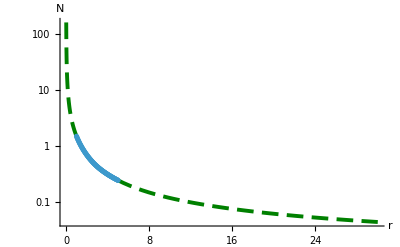

```mathematica
A=Plot[Evaluate[NN[r]/.s],{r,rMin,rMax+dr},Background->White,PlotRange->{ All,Automatic},
AxesLabel->{"r","N"},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150}];
A2=Plot[Evaluate[gg[r]/.s],{r,rMin,rMax+dr},Background->White,PlotRange->{ All,Automatic},
AxesLabel->{"r","N"},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150}];
A3=LogPlot[Evaluate[φ[r]/.s],{r,rMin,rMax+dr},Background->White,PlotRange->{ All,All},
AxesLabel->{"r","N"},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150}];
B=ListLogPlot[dataN];
Show[A3,B]
```

```mathematica
(*nlm=NonlinearModelFit[dataN,sN[r]/.s,{Subscript[a, 0],Subscript[a, -1]},r]*)
```

```mathematica
nlm=NonlinearModelFit[dataN,sϕ[r]/.β->βet,{Subscript[a, 0],Subscript[a, -1]},r]
parV=nlm["BestFitParameters"]
```

FittedModel[…]

{a_0→-0.109393,a_-1→1.59271}

```mathematica
F=Plot[sN[r]/.s/.parV/.β->βet,{r,rMin,5},PlotStyle->Red];
G=Plot[sG[r]/.s/.parV/.β->βet,{r,rMin,5},PlotStyle->Red];
H=LogPlot[sϕ[r]/.s/.parV/.β->βet,{r,rMin,10},PlotStyle->Red];
```

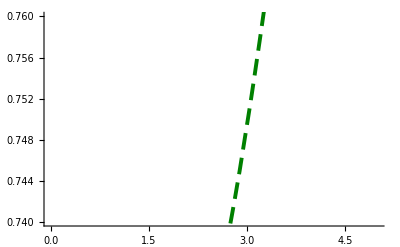

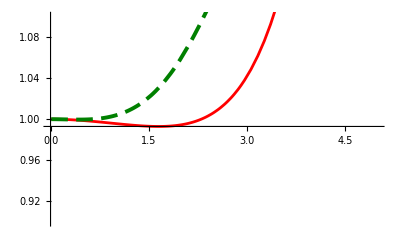

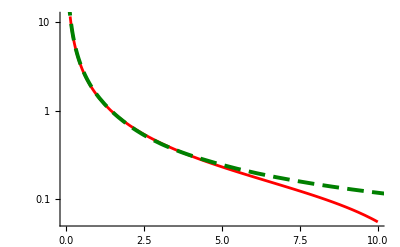

```mathematica
Show[{F,A},PlotRange->{{0,5},{0.74,0.76}}]
Show[{G,A2},PlotRange->{{0,5},{0.9,1.1}}]
Show[{H,A3}]
```

```mathematica
(*Series asintótica*)
JN=Plot[nRmax/.β->βet/.{Subscript[a, 0]->ϕrMax,Subscript[a, 1]->a1,Subscript[g, 1]->g1},{r,rMax,rMax+dr},PlotStyle->{Dotted,Red}];
Jg=Plot[gRmax/.β->βet/.{Subscript[a, 0]->ϕrMax,Subscript[a, 1]->a1,Subscript[g, 1]->g1},{r,rMax,rMax+dr},PlotStyle->{Dotted,Red}];
Jϕ=LogPlot[ϕRmax/.β->βet/.{Subscript[a, 0]->ϕrMax,Subscript[a, 1]->a1,Subscript[g, 1]->g1},{r,rMax,rMax+dr},PlotStyle->{Dotted,Red}];
```

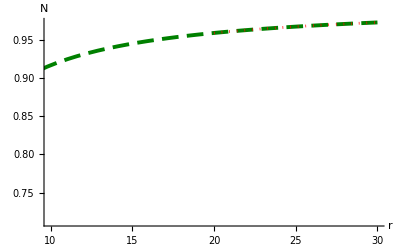

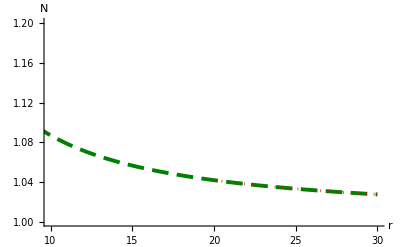

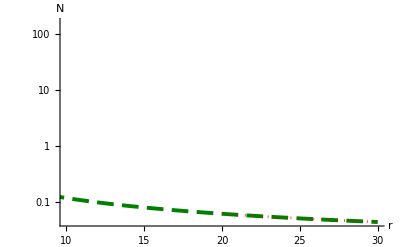

```mathematica
Show[{A,JN},PlotRange->{{rMax-dr,rMax+dr},All}]
Show[{A2,Jg},PlotRange->{{rMax-dr,rMax+dr},All}]
Show[{A3,Jϕ},PlotRange->{{rMax-dr,rMax+dr},All}]
```

```mathematica
(*Interpretación*)
```

```mathematica
(*{g1, ϕrMax, a1}*)
```

```mathematica
ClearAll[ β,βet ]
```

```mathematica
M[r]
```

1/2 r (1-1/gg[r]^2)

```mathematica
eqM=(M[r]/.gg[r]->gRmax)==MrMax//Simplify//Expand
```

960 MrMax r^4+240 r^3 a_1^2-1920 β a_0 a_1^3-(1920 β a_1^4)/r+480 r^4 g_1-3840 r β a_0 a_1 g_1-120 r^2 a_1^2 g_1-3840 β a_1^2 g_1+(576 β a_0 a_1^3 g_1)/r+5 a_1^4 g_1+80 r a_1^2 g_1^2+(2016 β a_1^2 g_1^2)/r-(12 a_1^4 g_1^2)/r-60 a_1^2 g_1^3+(48 a_1^2 g_1^4)/r==0

```mathematica
solg1=Solve[eqM,Subscript[g, 1]]
```

```mathematica
(*test*)
ClearAll[rMin,rMax, βet,β ,ϕrMax,g1, a1]
dat={};
datM={0.9949500001716127}(*Subdivide[.5,0.98,5]*);
(*rMin=10^-2;rMax =100;βet=5;ϕrMax=0.1;a1=2;*)
(*
datM=Subdivide[0.5,2.8,20];
rMin=10^-2;rMax =100;βet=5;ϕrMax=0.1;a1=2;*)
rMin=10^-5;rMax =100;βet=0.5;ϕrMax=0.1;a1=2.;
Do[
temp=solg1/.MrMax->datM[[i]]/.Subscript[a, 1] ->a1/.r->rMax/.β->βet/. Subscript[a, 0]->ϕrMax;
(*Print[temp];*)
temp2=nRmax/.Subscript[a, 1] ->a1/.r->rMax/.β->βet/. Subscript[a, 0]->ϕrMax/.temp;
Print[temp2];
AppendTo[dat,N@{rMin,rMax,βet,ϕrMax,a1,temp[[2,1,2]],datM[[i]]}]
,{i,1,Length[datM]}]
```

{0.+5.20166 ⅈ,0.989899,4.85682-2.60771 ⅈ,4.85682+2.60771 ⅈ}

```mathematica
dat
```

{{0.00001,100.,0.5,0.1,2.,-2.01011,0.99495}}

```mathematica
dat={{10^-5,100,1,0.1,2,-2.0,0.973}}
```

{{1/100000,100,1,0.1,2,-2.,0.973}}

```mathematica
s=NDSolve[{{-(NN[r]^2 φ'[r]^2)/(2 gg[r]^2)+(NN[r]^2 (gg[r]^2 (-gg[r]+gg[r]^3+2 r gg'[r])+8 (-β gg[r] (-1+gg[r]^2) φ'[r]^2+β φ[r] ((-3+gg[r]^2) gg'[r] φ'[r]-gg[r] (-1+gg[r]^2) φ''[r]))))/(r^2 gg[r]^5)==0,1/2 r ((r φ'[r]^2)/gg[r]^2+(2 (-gg[r]^2 gg'[r] (NN[r]+r NN'[r])+24 β φ[r] gg'[r] NN'[r] φ'[r]+gg[r]^3 (NN'[r]+r NN''[r])-8 gg[r] (β φ[r] φ'[r] NN''[r]+NN'[r] (β φ'[r]^2+β φ[r] φ''[r]))))/(gg[r]^5 NN[r]))==0,(8 β φ[r] ((-3+gg[r]^2) gg'[r] NN'[r]-gg[r] (-1+gg[r]^2) NN''[r]))/(r^2 gg[r]^5 NN[r])+(-gg'[r] φ'[r]+gg[r] ((2/r+NN'[r]/NN[r]) φ'[r]+φ''[r]))/gg[r]^3==0}/.β->0.5,{NN[100/Sqrt[2]]==0.9800003333333334,NN'[100/Sqrt[2]]==0.00019999,gg[100/Sqrt[2]]==0.980101,φ[100/Sqrt[2]]==0.12020233333333333,φ'[100/Sqrt[2]]==-0.00020407}(*{NN[100.]==0.9901205264728736,NN'[100.]==0.00009928051760593164,gg[100.]==1.0098743521804703,φ[100.]==0.12019853815228607,φ'[100.]==-0.00020399000643837086}*)},CoefFunctionsList[[1]],{r,rMin,rMax+dr},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All]
```

NDSolve::ndsz: At r == 1.82893, step size is effectively zero; singularity or stiff system suspected.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

```mathematica
(*Ejemplo*)
datSol={};
Do[
ClearAll[rMin,rMax, βet,β ,ϕrMax,g1, a1];
{rMin,rMax,βet,ϕrMax,a1,g1,Masa}=dat[[i]];
dr=10;
s=NDSolve[{EqsList[[1]],BCList[[1]]}/.β->βet,CoefFunctionsList[[1]],{r,rMin,rMax+dr},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All];
AppendTo[datSol,s]
,{i,1,Length[dat]}]
```

```mathematica
(*Masa*)
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

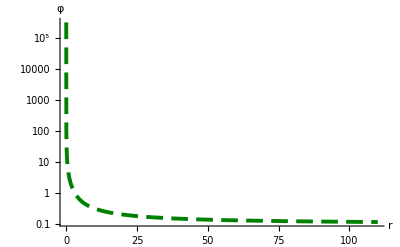
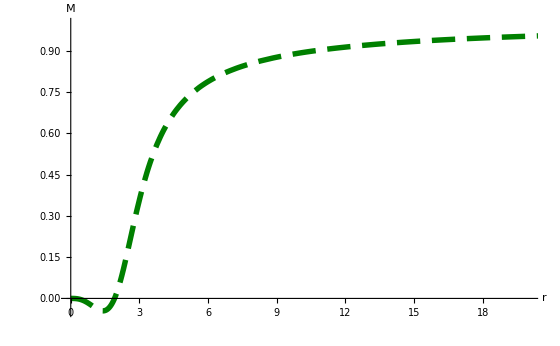
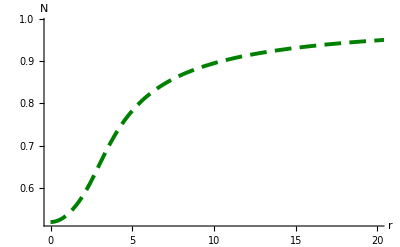
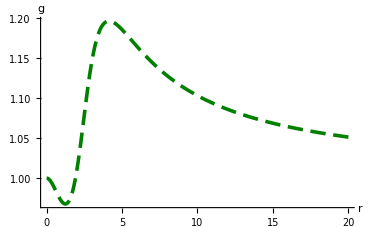

```mathematica
ele={φ[r], M[r],NN[r],gg[r]};
eleLab={"φ", "M", "N", "g"};
Table[If[i==1,LogPlot[{Evaluate[ele[[i]]/.datSol]},{r,rMin,rMax+dr},Background->White,PlotRange->{ {0,rMax+dr},All},
AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150}],Plot[{Evaluate[ele[[i]]/.datSol]},{r,rMin,rMax+dr},Background->White,PlotRange->{ {0,20},All},
AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150},AxesOrigin->{0,0}]],{i,4}]
```

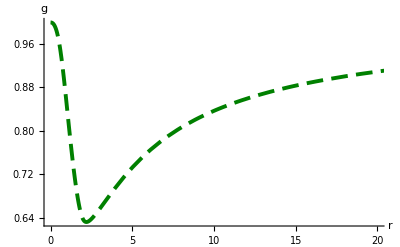

```mathematica
Plot[{Evaluate[gg[r]/.s]},{r,rMin,rMax+dr},Background->White,PlotRange->{ {0,20},All},
AxesLabel->{"r","g"},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},ImageSize->{Automatic,150},AxesOrigin->{0,0}]
```

```mathematica
temp=(M[rMax+dr]/.datSol)*0.9;
dataMR={};
Do[
sol=datSol[[i]];m99=temp[[i,1]];
rot=Last@FindRoot[M[r]==m99/.sol,{r,20}];
AppendTo[dataMR,{rot[[2]],m99}]
,{i,1,Length[datSol]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-2.33423} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.06134} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.6469} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

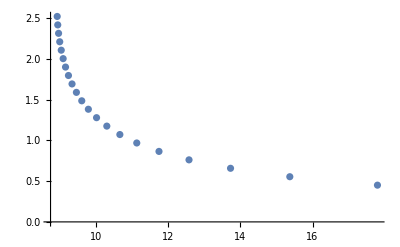

```mathematica
ListPlot@dataMR
```

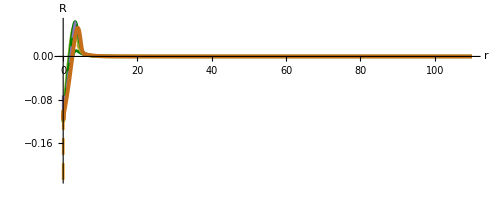

```mathematica
Plot[{Evaluate[RicciScalarEq/.datSol]},{r,rMin,rMax+dr},Background->White,PlotRange->{ {0,rMax+dr},All},
AxesLabel->{"r","R"},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},AspectRatio->Automatic]
```

```mathematica
(*valor teorico*)
-9./(16β)
```

-0.1125